Created by: ruebenko on 12-17-2018 12:40:58

### Categorization

Tutorial

Applications

Applications`

FEMAddOns/tutorial/PorousMediaEnergyTransport

Synonyms

FEA

### Keywords

Porous media

energy transport

multiple regions

discontinuities

convective diffusion

partial differential equation

PDE

Details

## Porous Media Energy Transport: PDE in multiple regions with discontinuities

Dr. Timothy E. Laska

-Graphics-

### Introduction

This notebook is based on a wolfram community post that was subsequently moved to a standalone staff pick.

Solving a coupled convective diffusive PDE in multiple regions with discontinuous physical properties can be quite challenging. In the end, I was pleasantly surprised that I was able to “model” this system and obtain reasonable results without too much difficulty. I am documenting my path here in the hopes that someone will find it useful.

### Preliminaries

I agree that there is no analytical solution to this system of coupled PDEs, and that a numerical solution is in order. The solution to the simplest convection-diffusion equation (NumberedEquation) for a parallel plate channel with fully developed uniform flow subjected to a uniform heat flux was shown to be an infinite series [Sparrow and Siegel, 1960, pg 167]

ρ C_p v_x (∂T)/(∂x)= k(∂^2 T)/(∂y^2)

For a coupled problem, I would presume that the infinite series coefficients would depend on the infinite series coefficients of the other variables making it intractable. [Ouyang et al] obtain an approximate solution with an infinite series solution to a thermally developing Darcy flow in porous media.

In the FEM, it is very easy to over constrain or under constrain a system leading to bizarre results. The developers of particular tools usually have developed a framework that facilitates the construction and solving of models. It is best to operate within that framework so that we can create a functioning model with least amount of effort.

Also, in the FEM, the mesh is critical to finding an accurate solution. In your case, you have two regions with distinct physical properties. We expect that there will be extreme changes in behavior at the interface of the two regions so we will want to resolve that area with a finer mesh.

Finally, I would recommend to start small and build complexity verifying and validating along the way.

### System Description

I always like to begin with a picture of the system I am trying to model. My understanding is that there is a fluid flowing over a porous material as shown in the picture below. The flow in the x direction is assumed to be laminar parabolic flow in the fluid domain and constant uniform in the porous domain.

```mathematica
ht = 1;
len = 2;
r = ht/8;
top = r;
bot = r-ht;
left = 0;
right = len;
v = Piecewise[{{0.75,#≤-r},{2(1-(#/r)^2),#>-r}}]&;
vp = Piecewise[{{#1,#2≤-r},{#1 -(1-(#2/r)^2),#2>-r}}]&;
DensityPlot[v[y],{x,0,1},{y,r,-3r},MeshFunctions->{vp},Mesh->10,MeshStyle->{Thick},AspectRatio->Automatic,PlotPoints->200,PlotRange->All,ColorFunction->ColorData["LightTemperatureMap"],PlotRangePadding->{{0.1,0},{0.1,0}},Frame->False,ImageSize->{640}]
```

Physically, there must be an impermeable solid barrier between the two domains otherwise we would expect some flow in the Y direction. We will take advantage of this fact later.

### Porous Media Domain Only

#### Porous Media Energy Transport Equations

As stated previously, the developers have created a framework to facilitate FEM modeling and simulation. For me, I find it often is easier to start over with that in mind than to start in the middle.

The equations below for energy transport with Local Thermal Non-Equilibrium (LTNE) were taken from [Nield and Bejan pg 32 equations 2.11-12 ] look formally similar to yours if we eliminate the transient and volumetric source terms shown in Red. If they are not, you should be able to follow the logic to develop your own

(1-ϵ)(ρ (Ĉ)_p)_s(∂T_s)/(∂t) + (ρ (Ĉ)_p)_s(v_s·∇T_s) - (1-ϵ)∇·k_s∇T_s -(1-ϵ)q'''_s - h(T_f - T_s) | = | 0

ϵ(ρ (Ĉ)_p)_f(∂T_f)/(∂t) + (ρ (Ĉ)_p)_f(v·∇T_f) - ϵ∇·k_f∇T_f - ϵ q'''_f - h(T_s - T_f) | = | 0

Assuming steady-state and eliminating the volumetric sources terms we obtain

(ρ (Ĉ)_p)_s(v_s·∇T_s) - (1-ϵ)∇·k_s∇T_s - h(T_f - T_s) | = | 0

(ρ (Ĉ)_p)_f(v·∇T_f) - ϵ∇·k_f∇T_f - h(T_s - T_f) | = | 0

Normally, we assume that the solid is fixed v_s={0,0}, but in this case we will retain it to use it to create an interface mixing rule. Otherwise, the solid density and heat capacity drops out of the equation and solid should dominate the mixing rule if the fluid is a gas because the density is >1000x higher.

#### Dimensional Analysis

When possible, I prefer to work with dimensionless equations. It helps reduce the equations to the minimum number of independent dimensionless parameters. To make the system dimensionless, we divide the variables by characteristic variables and perform some factoring so the left hand and right hand side of the equations are dimensionless. Dimensionless temperatures and coordinates are defined as:

Θ_s | = | (T_s-T_0)/T_C |   | T_s | = | T_C Θ_s + T_0
Θ_f | = | (T_f-T_0)/T_C |   | T_f | = | T_C Θ_f + T_0
v_s | = | v/v_0 |   | v | = | v_s v_0
x_s | = | x/D |   | x | = | D x_s
y_s | = | y/D |   | y | = | D y_s
T_C | = | (q_0 D)/k_f |   |   |   |

Generally, I would make the substitutions and perform the algebra manually. Let’s see if we can use Mathematica to help. First, we will use pdConv from this blog post to beautify the partial differential equations.

```mathematica
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__] :>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:> Sequence[],{var_,1}:> {var}}]]
```

Let’s look at the left hand side of equation (NumberedEquation) and recast it as an anonymous function where slots 1 and 2 correspond to T_s & T_f, respectively.

```mathematica
lhsf = (rhof cpf{vx,vy}.∇_{x,y} #2-ϵ kf ∇_{x,y}^2 #2- h(#1-#2))&;
```

Plugging in the solid and fluid temperature, we recover the LHS of equation (NumberedEquation).

```mathematica
lhsf[ts[t,x,y], tf[t,x,y]]//pdConv
```

cpf rhof (vx (∂tf(t,x,y))/(∂x)+vy (∂tf(t,x,y))/(∂y))-h (ts(t,x,y)-tf(t,x,y))-kf ϵ ((∂^2 tf(t,x,y))/(∂x^2)+(∂^2 tf(t,x,y))/(∂y^2))

Now, we replace the temperature functions with their dimensionless counterparts and replace the independent dimensioned variables with the dimensionless counterparts.

```mathematica
lhsfd = lhsf[tempchar tss[t/tc,x/d,y/d]+temp0,tempchar tfs[t/tc,x/d,y/d]+temp0]/.{x->xs d, y -> ys d, t-> ts tc,vx -> vxs  v0, vy->vys v0};
lhsfd//pdConv
```

cpf rhof ((tempchar v0 vxs (∂tfs(ts,xs,ys))/(∂xs))/d+(tempchar v0 vys (∂tfs(ts,xs,ys))/(∂ys))/d)-kf ϵ ((tempchar (∂^2 tfs(ts,xs,ys))/(∂xs^2))/d^2+(tempchar (∂^2 tfs(ts,xs,ys))/(∂ys^2))/d^2)-h (tempchar tss(ts,xs,ys)-tempchar tfs(ts,xs,ys))

If we multiply the equation by d/(cpf rhof tempchar v0), the equation will be dimensionless since the leftmost term will be composed of dimensionless variables. We can clean this up further by collecting the h and kf terms.

```mathematica
Collect[lhsfd d/(rhof cpf tempchar v0),{h,kf},Simplify]//pdConv
```

(d h (tfs(ts,xs,ys)-tss(ts,xs,ys)))/(cpf rhof v0)-(kf ϵ ((∂^2 tfs(ts,xs,ys))/(∂xs^2)+(∂^2 tfs(ts,xs,ys))/(∂ys^2)))/(cpf d rhof v0)+vxs (∂tfs(ts,xs,ys))/(∂xs)+vys (∂tfs(ts,xs,ys))/(∂ys)

To extract the coefficients, I will define a list of operators as shown in the following.

```mathematica
op = ({#3.#2@@#4#4[[2;;]],#2@@#4#4[[2;;]],-(#1@@#4-#2@@#4)})&;
funcsFluid = {tss,tfs,{vxs,vys},{ts,xs,ys}};
funcsSolid = {tfs,tss,{vsxs,vsys},{ts,xs,ys}};
termsFluid = (op @@ funcsFluid);
termsSolid = (op @@ funcsSolid);
termsFluid//pdConv
```

{vxs (∂tfs(ts,xs,ys))/(∂xs)+vys (∂tfs(ts,xs,ys))/(∂ys),(∂^2 tfs(ts,xs,ys))/(∂xs^2)+(∂^2 tfs(ts,xs,ys))/(∂ys^2),tfs(ts,xs,ys)-tss(ts,xs,ys)}

Now, we can collect coefficients in terms of the operator lists.

```mathematica
Coefficient[Collect[lhsfd d/(rhof cpf tempchar v0),{h,kf},Simplify],termsFluid]
```

{1,-(kf ϵ)/(cpf d rhof v0),(d h)/(cpf rhof v0)}

In this case, my approach to dimensional analysis will be to convert the dimensionless factors to ratios of characteristic timescales of physical processes that will in turn be dimensionless. Let’s look at the diffusive term or second coefficient.

ϵ(k/(ρ (Ĉ)_p))_f(1/D)(D/D)1/v_0= ϵ α_f/D^2 D/v_0= ϵ τ_conv/τ_cond = ϵ γ

τ_cond=D^2/((k/(ρ (Ĉ)_p))_f) = D^2/α_f (Conduction Timescale)

τ_conv = D/v_0 (Convective Timescale)

Similarly, we will operate on the collection of terms preceding the film coefficient or third coefficient.

h/((ρ (Ĉ)_p)_f)D/v_0=τ_conv/τ_film = η

τ_film=((ρ (Ĉ)_p)_f)/h (Film Coefficient Timescale)

We will perform the same operations for the solid temperature equation (NumberedEquation).

```mathematica
lhss = (rhos cps{vsx,vsy}.∇_{x,y} #1-(1-ϵ) ks ∇_{x,y}^2 #1- h(#2-#1))&;
lhssd = lhss[tempchar tss[t/tc,x/d,y/d]+temp0,tempchar tfs[t/tc,x/d,y/d]+temp0]/.{x->xs d, y -> ys d, t-> ts tc,vsx -> vsxs v0, vsy->vsys v0};
Coefficient[Collect[lhssd d/(rhof cpf tempchar v0),{h,ks},Simplify],termsSolid]
```

{(cps rhos)/(cpf rhof),(ks (-1+ϵ))/(cpf d rhof v0),(d h)/(cpf rhof v0)}

We will rearrange the collection of terms before the diffusive term or second coefficient.

(1- ϵ)k_s/k_f(k/(ρ (Ĉ)_p))_f(1/D)(D/D)1/v_0= (1 - ϵ)(k_s/k_f)τ_conv/τ_cond = (1 - ϵ) σ γ

Where

σ = (k_s/k_f)

The ratio of the density times heat capacity of the solid to fluid, shown in the first coefficient, we will represent with the variable, κ.

κ = ((ρ (Ĉ)_p)_s)/((ρ (Ĉ)_p)_f)

Finally, we end up with the dimensionless form of the equations

κ v_s^*(Ω)·∇^* Θ_s - (1 - ϵ(Ω))σ γ (∇^*)^2 Θ_s - η(Θ_f - Θ_s) = 0

v^*(Ω)·∇^* Θ_f - ϵ(Ω)γ (∇^*)^2 Θ_f - η(Θ_s - Θ_f) = 0

#### Neumann Boundary Condition (Flux) on Porous Boundary

When applying a flux on the porous boundary, there are different possible pathways through the fluid and solid. We must decide how to partition the heat flux. For parallel pathways, the effective conductivity is given by:

k_eff = (1 - ϵ) k_s + ϵ k_f ||1/k_f

k_eff/k_f = (1 - ϵ) σ + ϵ

We will use this as a guide to partition the flux accordingly.

x_f = ϵ/((1 - ϵ) σ + ϵ)

q_f = x_f q_tot

q_s = (1 - x_f) q_tot

### Modeling in Mathematica

With modeling, I am a firm believer that one should start simple, verify and validate the simulation results, and then build complexity. We will assume the convective diffusive heat equation has been previously validated.

Let’s start with a model of the porous domain only.

#### Mesh Creation

I followed the tutorial in the documentation for Element Mesh Creation to generate a mesh tailored to the physical situation. You will need to load the FEM package like so

```mathematica
Needs["NDSolve`FEM`"]
```

Let’s start with some definitions of a domain the is 1 unit high and 2 units long. We will also create some associations to collect surfaces and regions for clarity.

```mathematica
ht=1;
len=2;
top=ht;
bot=0;
left=0;
right=len;
bounds=<|inlet->1,hot->2|>;
regs=<|fluid->10,porous->20,interface->15|>;
```

We can create a boundary mesh using the ToBoundaryMesh command and mark unique edges to be used as boundary conditions later. All other edges will be assigned the default boundary condition of an insulated wall. The left edge colored Green will describe the inlet condition and the bottom edge colored Red will describe the heat flux condition. All other boundaries will be the default Neumann zero flux condition.

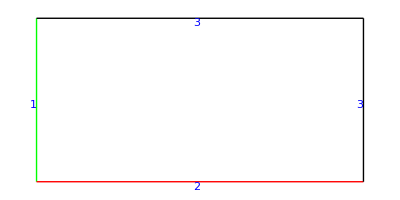

```mathematica
bmesh=ToBoundaryMesh["Coordinates"->{{left,bot}(*1*),{right,bot}(*2*),{right,top}(*3*),{left,top}(*4*)},"BoundaryElements"->{LineElement[{{1,2}(*bottom edge*)(*1*),{4,1}(*left edge*)(*2*),{2,3}(*3*),{3,4}(*4*)},{bounds[hot],bounds[inlet],3,3}]}];
bmesh["Wireframe"["MeshElementMarkerStyle"->Blue,"MeshElementStyle"->{Green,Red,Black}]]
```

Now, we will create an element mesh that will have a Red porous region with marker ID 20 (regs[porous]).

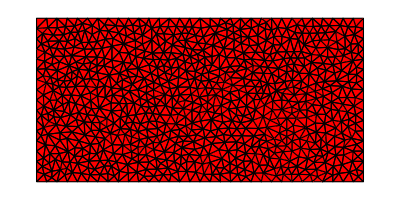

```mathematica
mesh=ToElementMesh[bmesh,"RegionMarker"->{{{(left+right)/2,(bot+top)/2},regs[porous],0.002}}];
mesh["Wireframe"["MeshElementStyle"->{FaceForm[Red]}]]
```

#### Implementation in NDSolve

By investing the time we did in mesh development, we can take advantage of some facilities provided by the Wolfram developers. First, we will convert our symbols to Latin for easier reading on the Web and define some initial parameters for testing.

ϵ = eps = p = 0.4

σ = s = 10

γ = g = 2

q_tot = qtot = 10

v_f = (6
0)

v_s = (0
0)

```mathematica
eps=0.4;
s=10;
g=2;
h=1/5;
mu=5000/h;
qtot=10;
(*Derived Parameters*)
xf=eps/((1-eps) s+eps);
hcapfrac=5000;
qf=xf qtot;
qs=(1-xf) qtot;
p=eps;
v={6,0};
vs={0,0};
fac=1;
```

We can also set our Neumann/flux boundary conditions for each state variable on the hot wall.

```mathematica
nvsolid=NeumannValue[qs,ElementMarker==bounds[hot]];
nvfluid=NeumannValue[qf,ElementMarker==bounds[hot]];
```

Likewise, we can set the inlet boundary for each state variable to 0 with Dirichlet conditions.

```mathematica
dcsolid=DirichletCondition[ts[x,y]==0,ElementMarker==bounds[inlet]];
dcfluid=DirichletCondition[tf[x,y]==0,ElementMarker==bounds[inlet]];
```

Recasting (NumberedEquation) and (NumberedEquation) into Mathematica format (remembering to put Neumann values on the right hand side where the 0 was), we obtain:

```mathematica
fluideqn=v.Inactive[Grad][tf[x,y],{x,y}]-p g Inactive[Laplacian][tf[x,y],{x,y}]-fac h (ts[x,y]-tf[x,y])==nvfluid;
solideqn=hcapfrac vs.Inactive[Grad][ts[x,y],{x,y}]-(1-p) g s Inactive[Laplacian][ts[x,y],{x,y}]-fac h (tf[x,y]-ts[x,y])==nvsolid;
```

Here are the equations in prettier form that I did before defining the coefficients.

```mathematica
solideqn
fluideqn
```

5000 {0,0}.ts[x,y]{x,y}Inactive+1/5 (-tf[x,y]+ts[x,y])-12. ts[x,y]{x,y}Inactive==NeumannValue[9.375,ElementMarker==2]

{6,0}.tf[x,y]{x,y}Inactive+1/5 (tf[x,y]-ts[x,y])-0.8 tf[x,y]{x,y}Inactive==NeumannValue[0.625,ElementMarker==2]

Now, we can solve on the element mesh we created earlier and do a 3D plot of the solution (Solid Temperature is translucent and has dashed lines).

```mathematica
ifun=NDSolveValue[{fluideqn,solideqn,dcfluid,dcsolid},{tf,ts},{x,y}∈mesh];
```

```mathematica
opac=If[ifun[[1]][0.5,0.5]>ifun[[2]][0.5,0.5],{0.25,1},{1,0.25}];
```

```mathematica
pltf=Plot3D[ifun[[1]][x,y],{x,y}∈mesh,PlotRange->All,PlotPoints->{200,200},ColorFunction->(Directive[Opacity[opac[[1]]],ColorData["DarkBands"][#3]]&),MeshFunctions->{#3&},Mesh->10,AxesLabel->Automatic,MeshStyle->{Black,Thick},ImageSize->Large];
plts=Plot3D[ifun[[2]][x,y],{x,y}∈mesh,PlotRange->All,PlotPoints->{200,200},ColorFunction->(Directive[Opacity[opac[[2]]],ColorData["DarkBands"][#3]]&),MeshFunctions->{#3&},Mesh->10,AxesLabel->Automatic,MeshStyle->{Black,Thick,Dashed},ImageSize->Large];
```

```mathematica
sz =300;
Grid[{{Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Front,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False],Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Left,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False]},{Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Top,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False],Show[{pltf,plts},ViewProjection->"Perspective",ViewPoint->{Above,Right,Front},ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False]}},Dividers->Center]
```

-Graphics-

#### Comparison to Another Code

Because we specified a low value of η, the heat transfer between the solid and fluid phase is poor leading to a large separation of temperatures. I think the plots look nice, but do they have any basis in reality? It is always good practice to validate models versus experiments or other codes when possible.
Fortunately, I have access to other codes and can say Mathematica compares favorably as shown below (T_s = thick lines). Having such agreement gives me confidence to continue to the more complex model.

We should note that T_s ≠ T_f|_(y=top) at the top of the insulated wall.

### Porous Media + Fluid Domain

How energy is transferred through the interface between two types of media can be a tricky business. Also, I don’t believe that Mathematica can have internal boundary conditions currently. However, Mathematica provides other machinery to create an “interface”. Recall earlier that I claimed that there must physically be a solid impermeable layer between the porous media and the fluid interface otherwise the porous media flow would short circuit into the fluid domain. So, let’s include a thin layer in the model. This thin layer will allow us to equilibrate the solid and fluid temperatures by drastically increasing the fluid-solid heat transfer coefficient to the correct heat capacity weighted value and ramping the porosity to unity at the fluid interface so that we don’t need to add another equation. A conceptual sketch is shown below.

We recast equations (NumberedEquation) and (NumberedEquation) in terms of some region dependent coefficients.

κ v_s^*(Ω)·∇^* Θ_s - (1 - ϵ(Ω))σ γ (∇^*)^2 Θ_s - μ(Ω)η(Θ_f - Θ_s) = 0

v^*(Ω)·∇^* Θ_f - ϵ(Ω)γ (∇^*)^2 Θ_f - μ(Ω)η(Θ_s - Θ_f) = 0

Where we define the region dependent functions as

v_s^*(Ω) = Piecewise[{{(0
0.001), Ω = Interface}, {(0
0), True}}]

v^*(Ω) = Piecewise[{{(6
0), Ω = Porous}, {(20(1-(y/r)^2
0), Ω = Fluid}, {(0
0.001), Ω = Interface}}]

ϵ(Ω) = Piecewise[{{ϵ_0, Ω = Porous}, {((1-ϵ_0)(r+thick+y))/thick+ϵ_0, Ω = Interface}, {1, True}}]

μ(Ω) = Piecewise[{{500000/η, Ω = Interface}, {1, True}}]

#### Mesh Creation for Porous, Fluid, and Coupling Interface

We will create a domain that is 1 unit in height by 2 units in length. The fluid (Green) will occupy the top 1/4 of the domain. The interface layer (Magenta) will be 1/40 the height. We will mark special boundaries and regions with unique IDs for boundary condition assignment and to change properties and mesh refine regions.

```mathematica
ht=1;
len=2;
r=ht/8;
top=r;
bot=r-ht;
left=0;
right=len;
thick=ht/40;
interfacef=-r;
interfaces=-r-thick;
buffer=1.5 thick;
(*Use associations for clearer assignment later*)
bounds=<|inlet->1,hot->2|>;
regs=<|porous->10,fluid->20,interface->15|>;
```

Boundary Mesh specification.

Coordinates

```mathematica
crds={{left,bot}(*1*),{right,bot}(*2*),{right,top}(*3*),{left,top}(*4*),{left,interfacef}(*5*),{right,interfacef}(*6*),{left,interfaces}(*7*),{right,interfaces}(*8*)};
```

Edges - 3 will be a default boundary

```mathematica
lelms={{1,7},{7,5},{5,4}(*left edge*)(*1*),{1,2}(*bottom edge*)(*2*),{2,8},{8,6},{6,3},{3,4},{5,6},{7,8}(*3*)};
boundaryMarker={bounds[inlet],bounds[inlet],bounds[inlet],bounds[hot],3,3,3,3,3,3};bcEle={LineElement[lelms,boundaryMarker]};
```

The boundary mesh.

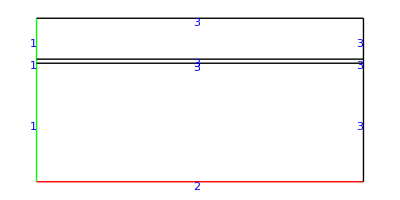

```mathematica
bmesh=ToBoundaryMesh["Coordinates"->crds,"BoundaryElements"->bcEle];
bmesh["Wireframe"["MeshElementMarkerStyle"->Blue,"MeshElementStyle"->{Green,Red,Black}]]
```

Full mesh generation.

Generate the mesh.

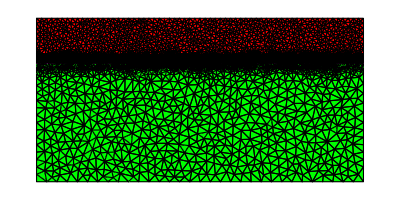

```mathematica
(*2D Regions*)
(*Identify Center Points of Different Material Regions*)
fluidCenter={(left+right)/2,0};
fluidReg={fluidCenter,regs[fluid],0.0005};
interfaceCenter={(left+right)/2,(interfaces+interfacef)/2};
interfaceReg={interfaceCenter,regs[interface],0.00005};
porousCenter={(left+right)/2,(bot+interfaces)/2};
porousReg={porousCenter,regs[porous],0.002};
meshRegs={fluidReg,interfaceReg,porousReg};
mesh=ToElementMesh[bmesh,"RegionMarker"->meshRegs,MeshRefinementFunction->Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];
If[y>(interfaces+interfacef)/2-buffer&&y<(interfaces+interfacef)/2+buffer,area>0.00005,area>0.01]]]];
mesh["Wireframe"["MeshElementStyle"->{FaceForm[Green],FaceForm[Magenta],FaceForm[Red]}]]
```

Mesh Zoomed into Interface Region

Zoomed in region.

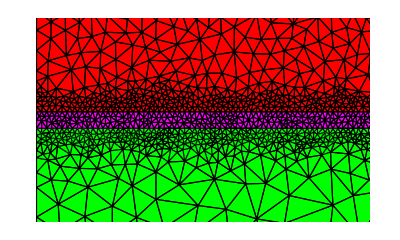

```mathematica
Show[mesh["Wireframe"["MeshElementStyle"->{FaceForm[Green],FaceForm[Magenta],FaceForm[Red]}]],PlotRange->{{0,0.5},{(interfaces+interfacef)/2-4 buffer,(interfaces+interfacef)/2+4 buffer}}]
```

#### NDSolve Setup and Solution

```mathematica
eps=0.4;
s=10;
g=2;
h=1/5;
mu=500000/h;
qtot=10;
xf=eps/((1-eps) s+eps);
kappa=500;
qf=xf qtot;
qs=(1-xf) qtot;
```

Region Dependent Properties with Piecewise Functions

```mathematica
p=Piecewise[{{eps,ElementMarker==regs[porous]},{(1-eps)/thick (y+(r+thick))+eps,ElementMarker==regs[interface]},{1,True}}];
v=Piecewise[{{{6,0},ElementMarker==regs[porous]},{{20 (1-(y/r)^2),0},ElementMarker==regs[fluid]},{{0,0.0001},ElementMarker==regs[interface]}}];
vs=Piecewise[{{{0,0.0001},ElementMarker==regs[interface]},{{0,0},True}}];
```

fac increases heat transfer coefficient

```mathematica
fac=With[{mu=mu},If[ElementMarker==regs[interface],mu,1]]
```

If[ElementMarker==15,2500000,1]

c matrices for coefficient form of pde.

```mathematica
cs = g(1-p)s IdentityMatrix[2];
cf = g p IdentityMatrix[2];
```

Neumann Conditions for the Hot Wall.

```mathematica
nvsolid=NeumannValue[qs,ElementMarker==bounds[hot]];
nvfluid=NeumannValue[qf,ElementMarker==bounds[hot]];
```

Dirichlet Conditions for the Left Wall.

```mathematica
dcsolid=DirichletCondition[ts[x,y]==0,ElementMarker==bounds[inlet]];
dcfluid=DirichletCondition[tf[x,y]==0,ElementMarker==bounds[inlet]];
```

Balance Equations for Fluid and Solid Temperature.

```mathematica
fluideqn=v.Inactive[Grad][tf[x,y],{x,y}]+(Inactive[Div][(-cf.Inactive[Grad][tf[x,y],{x,y}]),{x,y}])- fac h (ts[x,y]-tf[x,y])== nvfluid;
solideqn =  kappa vs.Inactive[Grad][ts[x,y],{x,y}]+(Inactive[Div][-cs.Inactive[Grad][ts[x,y],{x,y}],{x,y}])- fac h (tf[x,y]-ts[x,y])==nvsolid;
```

Solve the equation.

```mathematica
ifun=NDSolveValue[{fluideqn,solideqn,dcfluid,dcsolid},{tf,ts},{x,y}∈mesh];
```

Set opacity for higher temperature to be translucent so we can see the layer below

```mathematica
opac=If[ifun[[1]][0.5,(-r+bot)/2]>ifun[[2]][0.5,(-r+bot)/2],{0.25,1},{1,0.25}];
```

Plots

```mathematica
pltf=Plot3D[ifun[[1]][x,y],{x,y}∈mesh,PlotRange->All,PlotPoints->{200,200},ColorFunction->(Directive[Opacity[opac[[1]]],ColorData["DarkBands"][#3]]&),MeshFunctions->{#3&},Mesh->18,AxesLabel->Automatic,MeshStyle->{Black,Thick},ImageSize->Large];
plts=Plot3D[ifun[[2]][x,y],{x,y}∈mesh,PlotRange->All,PlotPoints->{200,200},ColorFunction->(Directive[Opacity[opac[[2]]],ColorData["DarkBands"][#3]]&),MeshFunctions->{#3&},Mesh->18,AxesLabel->Automatic,MeshStyle->{Black,Thick,Dashed},ImageSize->Large];
sz =300;
Rasterize[Grid[{{Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Front,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False],Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Left,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False]},{Show[{pltf,plts},ViewProjection->"Orthographic",ViewPoint->Top,ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False],Show[{pltf,plts},ViewProjection->"Perspective",ViewPoint->{Above,Right,Front},ImageSize->sz,Background->RGBColor[0.84,0.92,1.],Boxed->False]}},Dividers->Center]]
```

-Graphics-

#### Comparison to Another Code

Again, as shown below, the Mathematica solution compares qualitatively favorably to another code. The contour plots have similar shapes but Mathematica has about 40% higher temperatures, which could indicate that I dropped a factor ϵ somewhere in the setup of the other code, so a detailed debugging is probably in order. The implementation in the other code is slightly different due to different capabilities which I will elaborate. In the other code, the interface layer is a just a high thermal conductivity solid. I am able to set the porous-solid interface temperature to be equal to the porous temperature (solid-fluid bulk mix temperature).

Because I can set an interface boundary condition in the other code, I can remove the interface region and set the fluid boundary condition to the porous mean temperature and judge the effect of the interface region. As shown in the following image, the addition of the interface layer would not affect conclusions much.

### Summary

An exact analytical solution to an LTNE problem coupled to a fluid domain seems improbable.

Mathematica

Currently, I don’t think interface BCs can be defined in the FEM framework.

Does provide meshing features that allow the construction of an interface with finite thickness that might be used a workaround to this limitation.

Results

Porous Media Only Domain.

Quite easy to setup a mesh and identify unique boundaries and regions.

Straightforward to translate our system of PDEs created by hand into equations suitable for Mathematica.

Relatively easy to post process results using examples from documentation.

Solution compares favorably to another PDE code.

Combined Porous Media--Interface--Fluid Domains

Quite easy to setup a mesh with appropriate refinement and identify unique boundaries and regions.

Straightforward to translate our system of PDEs created by hand into equations suitable for Mathematica.

Relatively easy to post process results using examples from documentation.

Solution compares qualitatively favorably to another PDE code.

Additional study/debugging will be required to fully harmonize the results.

Could be a simple matter of missing a parameter or something deeper.

Conclusions

A prototype of a simple LTNE model was developed in Mathematica.

In modeling, there are many ways to skin a cat and this is just one possible way.

Additional model development and validation are necessary.

Mathematica provides enough features and tools that you can get close to what you need with some imagination.

More About

Related Tutorials

Related Wolfram Training Courses